```mathematica
(* Размер среды*)
CvI=3/2;CpI=5/2;gamma=CpI/CvI;
m=1.6726*10^(−27);
kB=1.3*10^(-23);
T=10^6;
Cs0 = Sqrt[kB * T / m];
len=100*10^6;
(*v1 = len/τ1 /Cs0;
v2 = len/τ2 /Cs0;
τ1 =2;
τ2 =0.1;
g0=(5 τ2)/(3 τ1);
goi=g0/gI;
*)
amp = 0.0;
wid =0.05;
pos = 0.8;
Nmax=5;
```

#### Начальные условия

```mathematica
InitialConds[] := Module[{},
Initial[x_,amp_,wid_,pos_]:=  amp ⅇ^(-(-pos+x)^2/(2 wid^2));
Initialdt[x_,amp_,wid_,pos_]:= +(amp ⅇ^(-(-pos+x)^2/(2 wid^2)) (-pos+x))/wid^2;

Initialdtt[x_,amp_,wid_,pos_]:=1/2 * amp (-(ⅇ^(-(-pos+x)^2/(2 wid^2)))/wid^2+(ⅇ^(-(-pos+x)^2/(2 wid^2)) (-pos+x)^2)/wid^4);
(*
Initialdt[x_,amp_,wid_,pos_]:=0;
Initialdtt[x_,amp_,wid_,pos_]:=0;*)]
```

#### Граничные условия и замена u(x,t) = U(x,t) + v(x,t)

```mathematica
BoundaryConds[] := Module[{},
freq=Pi*1.3;
amp2=1;

DecMask=0.9; (*параметр отвечающий, грубо говоря, за то, насколько сильно уменьшается маска за выбранную долю длины полуволны в точке pi/freq*)
RatioOfHalfLength=0.05; (*параметр отвечающий за долю длины полуволны в которой маска уменьшается с около 1 до около 0 в зависимости от параметра DecMask*)
pow=Log[(1+DecMask)/(1-DecMask)]*2/RatioOfHalfLength*freq/Pi;

(*BoundLeft[t_] =Sin[2*Pi/10/60*t];*)
BoundLeft[t_] =t^3*Exp[-10t];
(*BoundRight[t_] := Sin[freq*t]/(1+Exp[pow(t-Pi/freq)])*)
BoundRight[t_]=0;
U[x_,t_] := (BoundRight[t] - BoundLeft[t]) * x +BoundLeft[t];
]
```

### Модули для решения

#### Интегралы для определения констант

```mathematica
IntegralsForDuamel[] := Module[{},
Udt [x_,t_]= D[U[x,t], t];
Udtt [x_,t_]= D[D[U[x,t], t],t];
Udttt[x_,t_] =D[D[D[U[x,t], t],t],t];
UI3ro[amp_,wid_,pos_, n_,t_] =2*Integrate[(-Udttt[z, t]-v2 * Udtt[z,t])*Sin[Pi*n*z], {z, 0, 1}];]
```

```mathematica
IntegralsForInitialConds[] := Module[{},
I1InHro[amp_,wid_,pos_,n_]=2*Integrate[(Initial[z,amp,wid,pos]- U[z,0])*Sin[Pi*n*z], {z, 0, 1}];
I2InHro[amp_,wid_,pos_,n_]=2*Integrate[(Initialdt[z,amp,wid,pos]- Udt[z,0])*Sin[Pi*n*z], {z, 0, 1}];
I3InHro[amp_,wid_,pos_,n_]=2*Integrate[(Initialdtt[z,amp,wid,pos]- Udtt[z,0])*Sin[Pi*n*z], {z, 0, 1}];]
```

#### Кардано и корни

```mathematica
CardanoFormulas[] :=Module[{},
k[n_]=Pi*n ;
Acrd[v2_,d_,n_] = v2 + k[n]^2 d;
Bcrd[n_] = k[n]^2 gamma;
Ccrd[v2_,d_,gQ_,n_] = k[n]^2 gQ v2 + k[n]^4 d;
(*Задаем величину D1, которая напрямую связана с дискриминантом кубического уравнения по времени и опредлеяет какие корни по типу*)
P[v2_,d_,n_]=(3Bcrd[n]-Acrd[v2,d,n]^2)/9;                      
Q[v2_,d_,gQ_,n_]=1/54(2 Acrd[v2,d,n]^3-9Acrd[v2,d,n]*Bcrd[n]+27Ccrd[v2,d,gQ,n]);
D1[v2_,d_,gQ_,n_]=P[v2,d,n]^3+Q[v2,d,gQ,n]^2;
(*Ругает меня вольфрама, что скармливаю ей комплексную дичь*) 
A[v2_,d_,gQ_,n_]=If[D1[v2,d,gQ,n]>0,
CubeRoot[-Q[v2,d,gQ,n]+√D1[v2,d,gQ,n]],
N[(-Q[v2,d,gQ,n]+√D1[v2,d,gQ,n])^(1/3)]];
(*A[n_]=(-Q[n]+√D1[n])^(1/3);*)
(*A[n_]:=N[(-Q[n]+√D1[n])^(1/3)]*)
B[v2_,d_,gQ_,n_]=-P[v2,d,n]/A[v2,d,gQ,n];]
```

```mathematica
RootsCubicEquationODU[] :=Module[{},
wEI[v2_,d_,gQ_,n_]=-Acrd[v2,d,n]/3+A[v2,d,gQ,n]+B[v2,d,gQ,n];  
wAI[v2_,d_,gQ_,n_]=(Acrd[v2,d,n]/3+(A[v2,d,gQ,n]+B[v2,d,gQ,n])/2); 
wAR[v2_,d_,gQ_,n_]=(A[v2,d,gQ,n]-B[v2,d,gQ,n])/2 √3; (*
w1[n_]=If[D1[n]<0,I*Im[I*(-v2/3+A[n]+B[n])],I*(-v2/3+A[n]+B[n])];w2[n_]=If[D1[n]<0,I*Im[(A[n]-B[n])/2 √3- I*(v2/3+(A[n]+B[n])/2)],(A[n]-B[n])/2 √3- I*(v2/3+(A[n]+B[n])/2)];w3[n_]=If[D1[n]<0,I*Im[-(A[n]-B[n])/2- I*(v2/3+(A[n]+B[n])/2)],-(A[n]-B[n])/2- I*(v2/3+(A[n]+B[n])/2)];]*)
(*w1[v2_,d_,gQ_,n_]=-I*wEI[v2,d,gQ,n];
w2[v2_,d_,gQ_,n_]=wAR[v2,d,gQ,n]+I wAI[v2,d,gQ,n];
w3[v2_,d_,gQ_,n_]=-wAR[v2,d,gQ,n]+I wAI[v2,d,gQ,n];*)
w1[v2_,d_,gQ_,n_]=I*wEI[v2,d,gQ,n];
w2[v2_,d_,gQ_,n_]=wAR[v2,d,gQ,n]-I wAI[v2,d,gQ,n];
w3[v2_,d_,gQ_,n_]=-wAR[v2,d,gQ,n]-I wAI[v2,d,gQ,n];
]
```

#### Находим константы С

```mathematica
ConstsForHomogeneousSolution[]:=Module[{},
C2nro[v2_,d_,gQ_,n_]=(I3InHro[amp,wid,pos,n]+2*wAI[v2,d,gQ,n]*I2InHro[amp,wid,pos, n]-2*wAI[v2,d,gQ,n]*wEI[v2,d,gQ,n]*I1InHro[amp,wid,pos, n]-wEI[v2,d,gQ,n]^2*I1InHro[amp,wid,pos,n])/(-wAI[v2,d,gQ,n]^2-wAR[v2,d,gQ,n]^2-wEI[v2,d,gQ,n]^2-2*wAI[v2,d,gQ,n]*wEI[v2,d,gQ,n]);

C1nro[v2_,d_,gQ_,n_]=I1InHro[amp,wid,pos, n] - C2nro[v2,d,gQ,n];

C3nro[v2_,d_,gQ_,n_]=(I2InHro[amp,wid,pos, n]-wEI[v2,d,gQ,n] *I1InHro[amp,wid,pos, n] +(wAI[v2,d,gQ,n]+wEI[v2,d,gQ,n] )* C2nro[v2,d,gQ,n])/wAR[v2,d,gQ,n];

C3pro[v2_,d_,gQ_,n_] = ((I1InHro[amp,wid,pos, n]*w1[v2,d,gQ,n]-I*I2InHro[amp,wid,pos, n])w2[v2,d,gQ,n]-I*I2InHro[amp,wid,pos, n]w1[v2,d,gQ,n]-I3InHro[amp,wid,pos, n])/(w3[v2,d,gQ,n]^2-(w2[v2,d,gQ,n]+w1[v2,d,gQ,n])w3[v2,d,gQ,n]+w1[v2,d,gQ,n]w2[v2,d,gQ,n]);

C2pro[v2_,d_,gQ_,n_]=(I*I2InHro[amp,wid,pos, n]-w1[v2,d,gQ,n]*I1InHro[amp,wid,pos, n]-(w3[v2,d,gQ,n]-w1[v2,d,gQ,n])*C3pro[v2,d,gQ,n])/(w2[v2,d,gQ,n]-w1[v2,d,gQ,n]);

C1pro[v2_,d_,gQ_,n_] = I1InHro[amp,wid,pos, n]-C2pro[v2,d,gQ,n]-C3pro[v2,d,gQ,n];

C0ro[v2_,d_,gQ_,n_]=Sign[C2nro[v2,d,gQ,n]]*(√(C2nro[v2,d,gQ,n]^2+C3nro[v2,d,gQ,n]^2))/2;
]
```

#### Находим константы D для неоднородного уравнения Дирихле

```mathematica
ConstsForInHomogeneousSolution[]:= Module[{},
D2nro[v2_,d_,gQ_,n_, s_]=(UI3ro[amp,wid,pos, n,s])/(-wAI[v2,d,gQ,n]^2-wAR[v2,d,gQ,n]^2-wEI[v2,d,gQ,n]^2-2*wAI[v2,d,gQ,n]*wEI[v2,d,gQ,n]);

D1nro[v2_,d_,gQ_,n_, s_]=- D2nro[v2,d,gQ,n,s];

D3nro[v2_,d_,gQ_,n_,s_]=((wAI[v2,d,gQ,n]+wEI[v2,d,gQ,n] )* D2nro[v2,d,gQ,n,s])/wAR[v2,d,gQ,n];

D3pro[v2_,d_,gQ_,n_,s_] = -UI3ro[amp,wid,pos, n,s]/(w3[v2,d,gQ,n]^2-(w2[v2,d,gQ,n]+w1[v2,d,gQ,n])w3[v2,d,gQ,n]+w1[v2,d,gQ,n]w2[v2,d,gQ,n]);

D2pro[v2_,d_,gQ_,n_,s_]=(-(w3[v2,d,gQ,n]-w1[v2,d,gQ,n])*D3pro[v2,d,gQ,n,s])/(w2[v2,d,gQ,n]-w1[v2,d,gQ,n]);

D1pro[v2_,d_,gQ_,n_,s_] = -D2pro[v2,d,gQ,n,s]-D3pro[v2,d,gQ,n,s];
];
```

#### Слагаемые для решения

```mathematica
HomogeneousSolution[NMAX_]:=Module[{Nmax=NMAX},ro1[v2_,d_,gQ_,z_,t_, n_] = If[D1[v2,d,gQ,n]>0,
C1nro[v2,d,gQ,n]*Exp[wEI[v2,d,gQ,n]*t]*Sin[Pi*n*z]+Exp[-wAI[v2,d,gQ,n]*t]*(C2nro[v2,d,gQ,n]*Cos[wAR[v2,d,gQ,n]*t]+C3nro[v2,d,gQ,n]*Sin[wAR[v2,d,gQ,n]*t])*Sin[Pi*n*z],
(C1pro[v2,d,gQ,n]*Exp[-I*w1[v2,d,gQ,n]*t]+C2pro[v2,d,gQ,n]*Exp[-I*w2[v2,d,gQ,n]*t]+C3pro[v2,d,gQ,n]*Exp[-I*w3[v2,d,gQ,n]*t])*Sin[Pi*n*z]] ;

roHomogeneous[v2_,d_,gQ_,z_,t_]=Sum[ro1[v2,d,gQ,z,t,n],{n,Nmax}];]
```

```mathematica
ExpressionInDuamel[NMAX_]:=Module[{Nmax=NMAX},ro2[v2_,d_,gQ_,z_,t_,s_, n_] = If[D1[v2,d,gQ,n]>0,
D1nro[v2,d,gQ,n,s]*Exp[wEI[v2,d,gQ,n]*(t-s)]*Sin[Pi*n*z]+Exp[-wAI[v2,d,gQ,n]*(t-s)]*(D2nro[v2,d,gQ,n,s]*Cos[wAR[v2,d,gQ,n]*(t-s)]+D3nro[v2,d,gQ,n,s]*Sin[wAR[v2,d,gQ,n]*(t-s)])*Sin[Pi*n *z],
(D1pro[v2,d,gQ,n,s]*Exp[-I*w1[v2,d,gQ,n]*(t-s)]+D2pro[v2,d,gQ,n,s]*Exp[-I*w2[v2,d,gQ,n]*(t-s)]+D3pro[v2,d,gQ,n,s]*Exp[-I*w3[v2,d,gQ,n]*(t-s)])*Sin[Pi*n*z]] ;]
```

```mathematica
InHomogeneousSolutionAnalitical[NMAX_]:=Module[{Nmax=NMAX},roInHomogeneous[v2_,d_,gQ_,z_,t_]= Integrate[N[Sum[ro2[v2,d,gQ,z,t,s,n],{n,Nmax}]],{s,0,t} ]; ]
```

```mathematica
InHomogeneousSolutionNumeric[NMAX_]:=Module[{Nmax=NMAX},
NroInHomogeneous[v2_,d_,gQ_,z_,t_]:= NIntegrate[Sum[ro2[v2,d,gQ,z,t,s,n],{n,Nmax}],{s,0,t},Method->{"GaussKronrodRule","SymbolicProcessing"->0},AccuracyGoal->3];
]
```

#### Инициализация всех параметров

```mathematica
InitializateAllNeccessaryParams[tau1_,tau2_,taucond_]:=Module[{τ1=tau1, τ2 = tau2, τcond=taucond},
v1 = len/τ1 /Cs0;
v2 = len/τ2 /Cs0;
d = len/τcond/Cs0;
gQ=(5 τ2)/(3 τ1);
goi=gQ/gamma;

InitialConds[];
BoundaryConds[];
IntegralsForInitialConds[];
IntegralsForDuamel[];
CardanoFormulas[];
RootsCubicEquationODU[];
ConstsForHomogeneousSolution[];
ConstsForInHomogeneousSolution[];
]
```

#### Итоговое решение

```mathematica
SoluteEvolutionalEquationNumerical[tau1_,tau2_,taucond_,dZ_,dT_,TMIN_, TMAX_]:=Module[{dz=dZ,dt=dT,tmax=TMAX, tmin = TMIN,τ1=tau1, τ2 = tau2, τcond=taucond},
InitializateAllNeccessaryParams[τ1,τ2,τcond];
Print["InitializateAllNeccessaryParams was done"];
HomogeneousSolution[Nmax];
Print["HomogeneousSolution was done"];
ExpressionInDuamel[Nmax];
Print["ExpressionInDuamel was done"];
InHomogeneousSolutionNumeric[Nmax];
Print["InHomogeneousSolutionAnalitical was done"];
PointsOfSolution=Flatten[Table[{z,t,NroInHomogeneous[v2,d,gQ,z,t]+U[z,t]+roHomogeneous[v2,d,gQ,z,t]},{z,0,1,dz},{t,tmin,tmax,dt}],1]];
```

```mathematica
SoluteEvolutionalEquationAnalitical[tau1_,tau2_, taucond_]:=Module[{τ1=tau1, τ2 = tau2, τcond=taucond},
InitializateAllNeccessaryParams[τ1,τ2,τcond];
Print["InitializateAllNeccessaryParams was done"];
HomogeneousSolution[Nmax];
Print["HomogeneousSolution was done"];
ExpressionInDuamel[Nmax];
Print["ExpressionInDuamel was done"];
InHomogeneousSolutionAnalitical[Nmax];
Print["InHomogeneousSolutionAnalitical was done"];
ro[v2,d,gQ,z_,t_] = Re[N[roInHomogeneous[v2,d,gQ,z,t]+roHomogeneous[v2,d,gQ,z,t]+U[z,t]]];]
```

#### Извлекалка точек в один и тот же момент времени

```mathematica
GetPointsWithFixedT[Points_,t_]:=Module[
{points=Points},
For[i=Length[Points], i>=1,i--,
If[points[[i]][[2]]!=t,points=Delete[points,i] ,points[[i]]=Delete[points[[i]],2]];];

Return[points]]
```

```mathematica
ro0=10^-9;
```

```mathematica
tau1 = 40*60;
tau2=23*60;
taucond = (len)^2 CvI ro0 / (10^-11 T^(5/2));
```

```mathematica
Nz = 30;
Nt = 50;
dz = 1/(Nz - 1);
tmin =0;
tmax = 3;
dt = (tmax-tmin)/(Nt-1);
```

```mathematica
SoluteEvolutionalEquationNumerical[tau1,tau2,taucond,dz,dt,tmin,tmax];
```

InitializateAllNeccessaryParams was done

HomogeneousSolution was done

ExpressionInDuamel was done

InHomogeneousSolutionAnalitical was done

```mathematica
SoluteEvolutionalEquationAnalitical[tau1,tau2, taucond];
```

InitializateAllNeccessaryParams was done

HomogeneousSolution was done

ExpressionInDuamel was done

InHomogeneousSolutionAnalitical was done

```mathematica
PlotList = Table[Plot[ro[v2,d,gQ,z,t],{z,0,1}],{t,0,2,0.3}];
```

```mathematica
PlotList=Table[ListPlot[GetPointsWithFixedT[PointsOfSolution,t],PlotRange->{{0,1},{-0.005,0.005}},InterpolationOrder->3, Joined->True,Mesh->Full,PlotMarkers->{Automatic, Small}],{t,tmin,tmax,dt}];
```

```mathematica
ListAnimate[PlotList]
```

```mathematica
tau1 = 30*60;
tau2=5*60;
taucond = 448*60;
```

```mathematica
SoluteEvolutionalEquationAnalitical[tau1,tau2, taucond]
```

InitializateAllNeccessaryParams was done

HomogeneousSolution was done

ExpressionInDuamel was done

InHomogeneousSolutionAnalitical was done

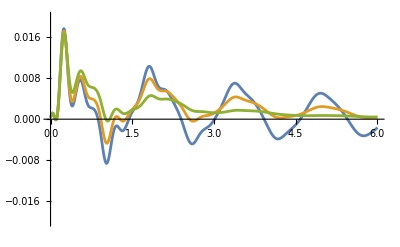

```mathematica
Plot[{ro[0.4431546107103961,0.022751241174864087,23/24,1/2,t],ro[0.8863092214207922,0.022751241174864087,0.31420765027322406,1/2,t],ro[v2,d,gQ,1/2,t]}, {t,0,6},PlotRange->{-0.02,0.02}]
```

```mathematica
{v2,d,gQ}
```

{0.443155,0.0227512,23/24}

```mathematica
v24023=0.4431546107103961;
d4023=0.022751241174864087;
gQ4023=23/24;
```

```mathematica
pl=Table[Plot[{ro[v2,d,gQ,z,t]}, {z,0,1},PlotRange->{-0.1,0.1}, PlotLegends->{"τ1 = 110 s, τ2 = 100 s, τcond = 10 000 s, u(0, t) = gauss"}],{t,0,5.4,0.04}];
```

```mathematica
la=ListAnimate[pl]
```